```mathematica
ClearAll["Global`*"]
```

### Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

#### Helper func

```mathematica
makeErrorData[x_,y_,yErr_]:=Module[{zeList,xy,errorB},
xy=Partition[Riffle[x,y],2];
errorB=Map[ErrorBar,yErr];
zeList=Partition[Riffle[xy,errorB],2]
];
```

```mathematica
Needs["ComputerArithmetic`"]
```

## Initialize orbit 1607 J-V, J_E-V data The diff is that we average by 4 this time

### pot offset (in V)?

```mathematica
potTFactor=0;
```

### And the data ...

```mathematica
time={"02:01:16.078","02:01:16.709","02:01:17.340","02:01:17.971","02:01:18.603","02:01:19.234","02:01:19.865","02:01:20.496","02:01:21.127","02:01:21.758","02:01:22.389","02:01:23.020","02:01:23.651","02:01:24.282","02:01:24.914","02:01:25.545","02:01:26.176","02:01:26.807","02:01:27.438","02:01:28.069","02:01:28.700","02:01:29.331","02:01:29.962","02:01:30.593","02:01:31.225","02:01:31.856","02:01:32.487","02:01:33.118","02:01:33.749","02:01:34.380","02:01:35.011","02:01:35.642","02:01:36.273","02:01:36.904","02:01:37.536","02:01:38.167","02:01:38.798","02:01:39.429","02:01:40.060","02:01:40.691","02:01:41.322","02:01:41.953","02:01:42.585","02:01:43.216","02:01:43.847","02:01:44.478","02:01:45.109","02:01:45.740","02:01:46.371","02:01:47.002","02:01:47.634","02:01:48.265","02:01:48.896","02:01:49.527","02:01:50.158","02:01:50.789","02:01:51.420","02:01:52.051","02:01:52.682","02:01:53.314","02:01:53.945","02:01:54.576","02:01:55.207","02:01:55.838","02:01:56.469","02:01:57.100","02:01:57.732","02:01:58.363","02:01:58.994","02:01:59.625","02:02:00.256","02:02:00.887","02:02:01.518","02:02:02.150","02:02:02.781","02:02:03.412","02:02:04.043","02:02:04.674","02:02:05.305","02:02:05.937","02:02:06.568","02:02:07.199","02:02:07.830","02:02:08.461","02:02:09.092","02:02:09.723","02:02:10.355","02:02:10.986","02:02:11.617","02:02:12.248","02:02:12.879","02:02:13.510","02:02:14.141","02:02:14.773","02:02:15.404","02:02:16.035","02:02:16.666","02:02:17.297","02:02:17.928","02:02:18.560","02:02:19.191","02:02:19.822","02:02:20.453","02:02:21.084","02:02:21.715","02:02:22.347","02:02:22.978","02:02:23.609","02:02:24.240","02:02:24.871","02:02:25.502","02:02:26.134","02:02:26.765","02:02:27.396","02:02:28.027","02:02:28.658","02:02:29.289","02:02:29.921","02:02:30.552","02:02:31.183","02:02:31.814","02:02:32.445","02:02:33.077","02:02:33.708","02:02:34.339","02:02:34.970","02:02:35.601","02:02:36.233","02:02:36.864","02:02:37.495","02:02:38.126","02:02:38.757","02:02:39.388","02:02:40.020","02:02:40.651","02:02:41.282","02:02:41.913","02:02:42.544","02:02:43.176","02:02:43.807","02:02:44.438","02:02:45.069","02:02:45.700","02:02:46.332","02:02:46.963","02:02:47.594","02:02:48.225","02:02:48.856","02:02:49.488","02:02:50.119","02:02:50.750","02:02:51.381","02:02:52.012","02:02:52.644","02:02:53.275","02:02:53.906","02:02:54.537","02:02:55.168","02:02:55.800","02:02:56.431","02:02:57.062","02:02:57.693","02:02:58.325","02:02:58.956","02:02:59.587","02:03:00.218","02:03:00.849","02:03:01.481","02:03:02.112","02:03:02.743","02:03:03.374","02:03:04.005","02:03:04.637","02:03:05.268","02:03:05.899","02:03:06.530","02:03:07.162","02:03:07.793","02:03:08.424","02:03:09.055","02:03:09.687","02:03:10.318","02:03:10.949","02:03:11.580","02:03:12.211","02:03:12.843","02:03:13.474","02:03:14.105","02:03:14.736","02:03:15.368","02:03:15.999","02:03:16.630","02:03:17.261","02:03:17.893","02:03:18.524","02:03:19.155","02:03:19.786","02:03:20.418","02:03:21.049","02:03:21.680","02:03:22.311","02:03:22.943","02:03:23.574","02:03:24.205","02:03:24.836","02:03:25.468","02:03:26.099","02:03:26.730","02:03:27.361","02:03:27.993","02:03:28.624","02:03:29.255","02:03:29.886","02:03:30.518","02:03:31.149","02:03:31.780","02:03:32.411","02:03:33.043","02:03:33.674","02:03:34.305","02:03:34.936","02:03:35.568","02:03:36.199","02:03:36.830","02:03:37.461","02:03:38.093","02:03:38.724","02:03:39.355","02:03:39.986","02:03:40.618","02:03:41.249","02:03:41.880","02:03:42.512","02:03:43.143","02:03:43.774","02:03:44.405","02:03:45.037","02:03:45.668","02:03:46.299","02:03:46.930","02:03:47.562","02:03:48.193","02:03:48.824","02:03:49.456","02:03:50.087","02:03:50.718","02:03:51.349","02:03:51.981","02:03:52.612","02:03:53.243","02:03:53.875","02:03:54.506","02:03:55.137","02:03:55.768","02:03:56.400","02:03:57.031","02:03:57.662"};
pots={407.68,407.68,344.96,940.80,282.24,282.24,282.24,282.24,344.96,344.96,344.96,282.24,282.24,282.24,344.96,282.24,282.24,282.24,282.24,282.24,282.24,282.24,282.24,344.96,407.68,282.24,344.96,282.24,282.24,407.68,407.68,689.92,689.92,1128.96,1128.96,1128.96,689.92,689.92,940.80,940.80,940.80,1379.84,1379.84,940.80,815.36,815.36,815.36,689.92,470.40,815.36,689.92,940.80,940.80,940.80,407.68,470.40,564.48,689.92,689.92,689.92,689.92,689.92,689.92,815.36,564.48,689.92,689.92,940.80,1128.96,940.80,884.80,592.48,566.72,602.56,553.28,1084.16,1751.68,1688.96,1886.08,1751.68,1491.84,1554.56,1688.96,777.28,790.72,741.44,1429.12,1232.00,665.28,665.28,678.72,949.76,949.76,708.40,592.48,567.84,741.44,692.16,790.72,1106.56,1330.56,1232.00,1330.56,1357.44,1581.44,1482.88,1671.04,1384.32,1482.88,1482.88,1482.88,1671.04,1581.44,1769.60,1630.72,1881.60,1630.72,1881.60,1881.60,2257.92,2257.92,2759.68,3261.44,3763.20,3763.20,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,3763.20,4515.84,4515.84,4515.84,5519.36,5519.36,4515.84,4515.84,3261.44,2759.68,2257.92,1881.60,1630.72,1128.96,1128.96,940.80,815.36,344.96,282.24,407.68,282.24,564.48,470.40,815.36,1379.84,1881.60,2257.92,2257.92,1630.72,1379.84,1128.96,1384.32,1581.44,2410.24,2410.24,2410.24,2661.12,2661.12,2661.12,3153.92,2858.24,2912.00,2661.12,3162.88,2912.00,2119.04,1769.60,2410.24,1671.04,1572.48,1671.04,1671.04,2020.48,2020.48,2266.88,2266.88,2464.00,2410.24,2858.24,3109.12,3655.68,3655.68,4049.92,4049.92,4032.00,4032.00,4032.00,3736.32,3539.20,3539.20,3539.20,3162.88,3162.88,3736.32,3539.20,3539.20,3736.32,3360.00,3162.88,3162.88,3342.08,3342.08,3498.88,3498.88,2800.00,2325.12,1881.60,1881.60,344.96,470.40,564.48,407.68,344.96,407.68,344.96,564.48,282.24,282.24,1128.96,1128.96,940.80,1128.96,407.68,282.24,282.24,1379.84,815.36,940.80,815.36,940.80,282.24,940.80,282.24,282.24,282.24,282.24,344.96,282.24,282.24,1379.84,344.96,344.96,407.68,470.40,344.96,282.24};
curs={0.443,0.381,0.400,0.356,0.353,0.288,0.217,0.373,0.314,0.337,0.402,0.308,0.201,0.199,0.133,0.233,0.166,0.169,0.178,0.596,0.229,0.438,0.670,1.405,1.407,0.395,0.104,0.131,0.500,1.145,1.473,1.614,1.489,2.619,2.488,1.543,1.007,0.997,1.111,1.318,1.430,2.460,1.954,1.357,0.835,0.624,0.247,0.162,0.165,0.176,0.145,0.171,0.190,0.266,0.420,0.755,0.849,0.929,1.045,1.055,0.960,0.900,0.814,1.004,1.005,0.952,0.961,1.126,1.045,1.261,0.777,0.884,0.649,0.412,0.558,0.617,0.837,0.786,0.733,0.701,0.788,0.873,0.777,0.678,0.537,0.522,0.405,0.396,0.404,0.393,0.519,0.526,0.463,0.457,0.518,0.608,0.613,0.595,0.655,0.648,0.713,0.857,0.798,1.129,1.224,1.417,1.425,1.261,1.388,1.427,1.443,1.683,1.575,1.519,1.170,1.186,0.914,1.148,1.110,1.213,1.315,1.585,1.913,2.163,2.486,2.430,2.591,2.637,2.387,2.262,2.344,2.030,2.064,2.194,3.582,4.924,5.407,5.627,5.219,4.690,4.253,3.906,3.509,2.756,2.830,2.388,2.350,1.958,0.755,0.462,0.098,0.048,0.077,0.278,0.949,1.341,1.776,2.314,2.185,1.431,1.193,0.677,0.656,0.800,0.898,0.828,0.859,0.940,1.042,0.888,0.923,0.798,1.094,0.844,1.187,0.941,0.753,0.818,0.964,0.740,0.788,0.859,0.874,0.787,0.828,0.858,0.919,0.929,0.964,0.996,1.030,1.315,1.283,1.360,1.380,1.416,1.326,1.451,1.682,1.852,1.966,1.823,1.869,1.767,1.553,1.586,1.545,1.670,1.586,1.542,1.497,1.870,1.904,1.913,1.869,1.878,1.681,1.425,1.371,2.006,3.038,3.490,3.041,2.593,2.938,2.536,4.619,2.203,0.715,0.569,0.792,0.709,0.730,1.140,1.400,1.168,0.508,0.586,0.673,0.706,0.914,1.384,0.797,0.940,1.163,0.974,0.731,1.303,1.213,1.223,1.022,1.047,1.228,1.982,1.810,1.597,1.336};
curErrs={0.026,0.035,0.029,0.039,0.027,0.031,0.025,0.030,0.022,0.030,0.029,0.032,0.017,0.029,0.034,0.066,0.027,0.050,0.032,0.036,0.018,0.037,0.037,0.059,0.052,0.063,0.030,0.014,0.026,0.040,0.043,0.051,0.044,0.065,0.071,0.056,0.045,0.038,0.037,0.053,0.046,0.068,0.062,0.055,0.044,0.030,0.028,0.019,0.025,0.027,0.022,0.020,0.029,0.029,0.027,0.032,0.035,0.044,0.040,0.044,0.047,0.039,0.044,0.050,0.046,0.053,0.046,0.059,0.070,0.068,0.042,0.053,0.063,0.042,0.041,0.034,0.051,0.041,0.034,0.037,0.045,0.047,0.043,0.065,0.047,0.037,0.038,0.048,0.043,0.062,0.040,0.051,0.054,0.044,0.043,0.045,0.074,0.051,0.059,0.026,0.027,0.026,0.026,0.029,0.031,0.038,0.034,0.033,0.038,0.038,0.037,0.041,0.043,0.041,0.033,0.035,0.033,0.035,0.033,0.035,0.039,0.046,0.048,0.046,0.060,0.054,0.053,0.057,0.056,0.056,0.056,0.060,0.064,0.071,0.084,0.116,0.122,0.137,0.124,0.129,0.099,0.089,0.086,0.072,0.070,0.067,0.066,0.061,0.037,0.029,0.011,0.010,0.014,0.032,0.042,0.052,0.066,0.080,0.075,0.052,0.056,0.045,0.038,0.037,0.051,0.044,0.041,0.047,0.047,0.046,0.070,0.049,0.079,0.055,0.054,0.061,0.057,0.048,0.051,0.051,0.066,0.051,0.048,0.045,0.049,0.054,0.058,0.062,0.059,0.059,0.053,0.077,0.079,0.087,0.082,0.090,0.112,0.103,0.101,0.108,0.114,0.117,0.114,0.127,0.179,0.134,0.093,0.098,0.109,0.112,0.129,0.160,0.144,0.153,0.116,0.076,0.084,0.127,0.080,0.061,0.040,0.059,0.056,0.054,0.040,0.050,0.068,0.054,0.036,0.035,0.043,0.040,0.046,0.050,0.058,0.076,0.087,0.150,0.083,0.107,0.085,0.089,0.150,0.056,0.043,0.055,0.037,0.052,0.047,0.048,0.058,0.068,0.046,0.075,0.060,0.072,0.059};
jes={0.298,0.246,0.258,0.262,0.240,0.193,0.142,0.246,0.183,0.204,0.204,0.173,0.146,0.147,0.132,0.191,0.140,0.164,0.157,0.312,0.174,0.262,0.369,0.660,0.761,0.231,0.106,0.141,0.324,0.727,0.975,1.177,1.194,2.619,2.779,1.707,0.973,0.943,1.157,1.413,1.564,3.246,2.605,1.481,0.872,0.556,0.256,0.203,0.202,0.198,0.178,0.198,0.248,0.297,0.412,0.673,0.797,0.887,1.034,1.057,0.994,0.974,0.894,1.137,1.045,1.039,1.045,1.459,1.322,1.407,0.620,0.586,0.480,0.301,0.397,0.438,0.608,0.543,0.512,0.505,0.544,0.579,0.525,0.466,0.415,0.388,0.289,0.283,0.281,0.261,0.356,0.366,0.326,0.336,0.385,0.431,0.440,0.439,0.505,0.516,0.608,0.784,0.723,1.175,1.281,1.464,1.572,1.409,1.506,1.504,1.572,1.962,1.735,1.812,1.956,2.082,1.592,2.192,2.186,2.548,2.952,3.999,5.441,6.827,8.725,9.140,10.112,10.042,9.136,8.720,8.653,7.230,7.551,8.009,13.617,19.492,19.109,18.375,14.677,11.324,8.566,6.235,5.396,3.428,2.804,2.233,2.027,1.447,0.435,0.276,0.085,0.042,0.063,0.190,0.769,1.780,3.038,4.677,4.450,2.308,1.693,0.794,0.743,0.976,1.170,1.117,1.200,1.346,1.633,1.341,1.549,1.291,1.948,1.412,2.309,1.636,0.997,1.048,1.257,0.945,1.090,1.131,1.211,1.204,1.240,1.308,1.431,1.390,1.347,1.431,1.746,2.561,2.470,2.665,2.697,2.892,2.763,3.070,3.426,4.073,4.321,3.852,3.694,3.536,3.158,3.329,3.146,3.506,3.126,2.902,2.932,3.983,4.038,4.421,4.468,3.397,2.844,2.298,2.192,2.624,2.943,2.960,2.520,2.128,2.151,2.046,3.792,1.854,0.802,0.704,0.986,0.837,0.942,1.223,1.209,0.962,0.646,0.718,0.798,0.825,1.046,1.413,0.915,0.973,0.997,0.837,0.703,1.190,1.270,1.132,1.155,0.997,1.045,1.323,1.291,1.163,1.107};
jeErrs={0.071,0.099,0.079,0.104,0.067,0.159,0.078,0.091,0.068,0.139,0.082,0.068,0.134,0.123,0.188,0.136,0.091,0.090,0.060,0.118,0.119,0.107,0.110,0.173,0.748,0.128,0.085,0.077,0.155,0.109,0.126,0.144,0.156,0.214,0.259,0.205,0.150,0.129,0.120,0.180,0.162,0.268,0.247,0.200,0.174,0.123,0.095,0.085,0.084,0.105,0.119,0.084,0.130,0.127,0.080,0.095,0.131,0.147,0.148,0.157,0.155,0.168,0.199,0.167,0.188,0.181,0.150,0.217,0.392,0.255,0.140,0.133,0.152,0.091,0.126,0.119,0.138,0.113,0.099,0.157,0.123,0.139,0.116,0.152,0.149,0.141,0.102,0.123,0.092,0.115,0.114,0.122,0.132,0.103,0.106,0.149,1.104,0.148,0.173,0.170,0.148,0.112,0.102,0.146,0.155,0.176,0.155,0.151,0.218,0.162,0.174,0.189,0.168,0.164,0.145,0.159,0.153,0.174,0.155,0.185,0.216,0.264,0.291,0.289,0.426,0.387,0.367,0.407,0.420,0.407,0.385,0.408,0.405,0.460,0.559,0.788,0.710,0.776,0.586,0.515,0.344,0.303,0.293,0.206,0.209,0.192,0.186,0.172,0.125,0.090,0.030,0.024,0.125,0.071,0.112,0.189,0.338,0.409,0.376,0.239,0.249,0.168,0.156,0.187,0.308,0.247,0.204,0.255,0.253,0.241,0.398,0.300,2.108,0.342,0.305,0.309,0.274,0.216,0.202,0.207,0.341,0.236,0.193,0.215,0.236,0.244,0.324,0.336,0.300,0.301,0.285,0.556,0.500,0.545,0.495,0.617,0.723,0.655,0.643,0.682,0.748,0.687,0.702,0.786,1.026,0.736,0.506,0.589,0.636,0.582,0.662,0.879,0.824,0.948,0.585,0.386,0.713,0.452,0.304,0.176,0.180,0.201,0.159,0.182,0.193,0.161,0.221,0.167,0.112,0.106,0.136,0.127,0.152,0.138,0.132,0.176,0.229,0.816,0.218,0.635,0.510,0.279,0.402,0.146,0.125,0.119,0.150,0.134,0.155,0.184,0.166,0.156,0.122,0.184,0.175,0.172,0.174};
```

## Manip plots to decide on indices to use

### Check out J-V relation

```mathematica
ind1Start=0;ind1End=120;ind1Init=100;ind2Init=132;(*Jim alt?*)
```

```mathematica
ind1Start=0;ind1End=144;ind1Init=137;ind2Init=150;(*Jim alt?*)
```

```mathematica
ind1Start=0;ind1End=178;ind1Init=162;ind2Init=198;(*Jim alt?*)
```

```mathematica
ind1Start=0;ind1End=150;ind1Init=72;ind2Init=198;(*Jim alt?*)
```

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],curs[[#1;;#2]],curErrs[[#1;;#2]]])&[ind1,ind2],AxesStyle->(FontSize->24),PlotRange->{{000,Max[pots]*1.1},{0,Max[curs]*1.1}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

### Check out energy flux–voltage relation

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],jes[[#1;;#2]],jeErrs[[#1;;#2]]])&[ind1,ind2],PlotRange->{{0,Max[pots]},{0,Max[jes]}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

The fits—J-V, J_E-V, and combined

## Initialize data for portions of arc in which we are interested

### Setup indices

```mathematica
inds1=Range[100,132];
```

```mathematica
inds2=Range[137,150];
```

```mathematica
inds2=Range[162,198]; (*Alt*)
```

```mathematica
inds3={3,4}~Join~inds2;
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{plotData1,plotData2,plotData3}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorData1,errorData2,errorData3}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{plotDataWts1,plotDataWts2,plotDataWts3}=(1/(curErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

Energy flux data

```mathematica
{jeData1,jeData2,jeData3}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorJe1,errorJe2,errorJe3}=(makeErrorData[pots[[#]],jes[[#]],jeErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{jeDataWts1,jeDataWts2,jeDataWts3}=(1/(jeErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

## Fits: Select indices to use, setup bounds and initial guesses

### Which to use?

```mathematica
useinds1=0; (*Else use inds2*)
```

### Bounds

```mathematica
minFitT=100;
maxFitT=5000;
minFitRB=3;
maxFitRB=1000000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

### Initial guesses

```mathematica
kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;
gFitRB1init=10;
gFitRB2init=10;
```

#### Init fit data

Maxwellian-ish thing?

```mathematica
If[useinds1==1,Print["Using inds1 ..."];indsInUse=inds1;jData=plotData1;jWts=plotDataWts1;jErrData=errorData1;jeData=jeData1;jeWts=jeDataWts1;jeErrData=errorJe1;,Print["Using inds2 ..."];indsInUse=inds2;jData=plotData2;jWts=plotDataWts2;jErrData=errorData2;jeData=jeData2;jeWts=jeDataWts2;jeErrData=errorJe2;];
```

Using inds2 ...

## Nonlinear J-V fits

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,10<kFitT<4000,3<kFitRB<1000000,1.501<kFitKappa<20};
gConstraints={0.01<gFitN<10,10<gFitT<4000,3<gFitRB<1000000};*)
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[jData,{kModel,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWts];
```

```mathematica
gFit=NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB,gFitRBinit}},pot,Weights->jWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWts]/kDOF};
```

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWts]/gDOF};
```

## Nonlinear J_E-V fits

### Initial guesses

```mathematica
(*kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;*)
```

```mathematica
(*gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;*)
```

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,100<kFitT<4000,3<kFitRB<1000,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,100<gFitT<4000,3<gFitRB<1000};*)
```

```mathematica
kModelJeV = JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModelJeV = JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFitJeV=NonlinearModelFit[jeData,{kModelJeV,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jeWts];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

```mathematica
gFitJeV=NonlinearModelFit[jeData,{gModelJeV,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitRBinit},{gFitRB,gFitRBinit}},pot,Weights->jeWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestJeVN,kBestJeVT,kBestJeVRB,kBestJeVKappa,kBestJeVChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeWts]/kDOF};
```

```mathematica
{gBestJeVN,gBestJeVT,gBestJeVRB,gBestJeVChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeWts]/gDOF};
```

## Now J-V and J_E-V fits simultaneously!

```mathematica
(*RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;*)
```

```mathematica
(*RBinit=kBestJeVRB;Tminit=kBestJeVT;nminit=kBestJeVN;kappainit=kBestJeVKappa;*)
```

```mathematica
combDat = Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=jWts~Join~jeWts;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]];
```

```mathematica
gCombFitModel[set_,pot_,gFitRB,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]];
```

```mathematica
kCombFit=NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB,kFitRBinit},{kFitT,kFitTinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->combWts];
```

```mathematica
gCombFit=NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB,gFitT,gFitN],gCombConstraints},{{gFitRB,gFitRBinit},{gFitT,gFitTinit},{gFitN,gFitNinit}},{set,pot},Weights->combWts];
```

```mathematica
kCombDOF=Length[combDat[[;;,1]]]-4;
```

```mathematica
gCombDOF=Length[combDat[[;;,1]]]-3;
```

```mathematica
{kCombRB,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF};
```

```mathematica
{gCombRB,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF};
```

Plots

### Setup plot ranges

```mathematica
minPot=Min[pots[[;;]] ]* 8/10;maxPot=6000;
```

```mathematica
minJ=0;maxJ=6;
```

```mathematica
minJe=0;maxJe=19.;
```

### Setup combined fit plots

```mathematica
parNames={"T_m : ","n_m : ","R_B : ","χ_red^2:"};
vSpace=0.5;
pTableFontSize=16;
```

```mathematica
JVRepl={gRB->gBestRB,gTm->gBestT,gnm->gBestN,gChi2->gBestChi2red,kRB->kBestRB,kTm->kBestT,knm->kBestN,kappa->kBestKappa,kChi2->kBestChi2red};
```

```mathematica
JeVRepl={gRB->gBestJeVRB,gTm->gBestJeVT,gnm->gBestJeVN,gChi2->gBestJeVChi2red,kRB->kBestJeVRB,kTm->kBestJeVT,knm->kBestJeVN,kappa->kBestJeVKappa,kChi2->kBestJeVChi2red};
```

```mathematica
combRepl={gRB->gCombRB,gTm->gCombT,gnm->gCombN,gChi2->gCombChi2red,kRB->kCombRB,kTm->kCombT,knm->kCombN,kappa->kCombKappa,kChi2->kCombChi2red};
```

```mathematica
(*gVals=MapThread[NumberForm,{({gTm,gnm,gRB}/.combRepl),{{3,0},{3,2},{3,1}}}];
kVals=MapThread[NumberForm,{({kTm,knm,kRB}/.combRepl),{{3,0},{3,2},{3,1}}}];*)
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gTm,gnm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JVRepl}~Join~{NumberForm[gChi2,3]/.JVRepl};
kJVVals=(MapThread[NumberForm,{({kTm,knm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JVRepl}~Join~{NumberForm[kChi2,3]/.JVRepl};
```

```mathematica
gJeVVals=(MapThread[NumberForm,{({gTm,gnm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JeVRepl}~Join~{NumberForm[gChi2,3]/.JeVRepl};
kJeVVals=(MapThread[NumberForm,{({kTm,knm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JeVRepl}~Join~{NumberForm[kChi2,4]/.JeVRepl};
```

```mathematica
gCombVals=(MapThread[NumberForm,{({gTm,gnm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.combRepl}~Join~{NumberForm[gChi2,4]/.combRepl};
kCombVals=(MapThread[NumberForm,{({kTm,knm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.combRepl}~Join~{NumberForm[kChi2,4]/.combRepl};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gJVVals~Join~{""}~Join~kJVVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
JeVParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gJeVVals~Join~{""}~Join~kJeVVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combParTable=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gCombVals~Join~{""}~Join~kCombVals}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combTitle=StringJoin@Riffle[time[[indsInUse[[{1,-1}]]]],"–"];
```

```mathematica
combFitJVPlot=Plot[Evaluate@(({JVMaxwellian[pot,gRB,gTm,gnm],JVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.combRepl),{3,3}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",combTitle],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[combParTable,Scaled[{0.12,0.7}]]];
```

```mathematica
combFitJeVPlot=Plot[Evaluate@(({JEVMaxwellian[pot,gRB,gTm,gnm],JEVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,23]];
```

```mathematica
combJVPlot=Show[combFitJVPlot,ErrorListPlot[jErrData,PlotStyle->Gray]];
```

```mathematica
combJeVPlot=Show[combFitJeVPlot,ErrorListPlot[jeErrData,PlotStyle->Gray]];
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
```

```mathematica
If[!FileExistsQ[dir],Print["Nei!"];CreateDirectory[dir];Print["Nå har du det!"],Print["Ja!"]]
```

Ja!

```mathematica
orbPref="Orb11694";
```

```mathematica
JVPref="JVFit";
JeVPref="JeVFit";
combPref="combJVJeVFit";
```

```mathematica
(*combJVPref="combJVJeVFit__JV";
combJeVPref="combJVJeVFit__JeV";*)
```

```mathematica
(*{JVFilename,JeVFilename,combJVFilename,combJeVFilename}=(ToString@StringForm["`1`__`2`__inds_`3`-`4`.png",orbPref,#,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combJVPref,combJeVPref}*)
```

```mathematica
If[potTFactor == 0,suffString="",suffString=ToString@StringForm["__`1`V_offset",potTFactor]];
```

```mathematica
{JVFilename,JeVFilename,combFilename}=(ToString@StringForm["`1`__`2``3`__inds_`4`-`5`.png",orbPref,#,suffString,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combPref}
```

{Orb11694__JVFit__inds_162-198.png,Orb11694__JeVFit__inds_162-198.png,Orb11694__combJVJeVFit__inds_162-198.png}

### J-V plot

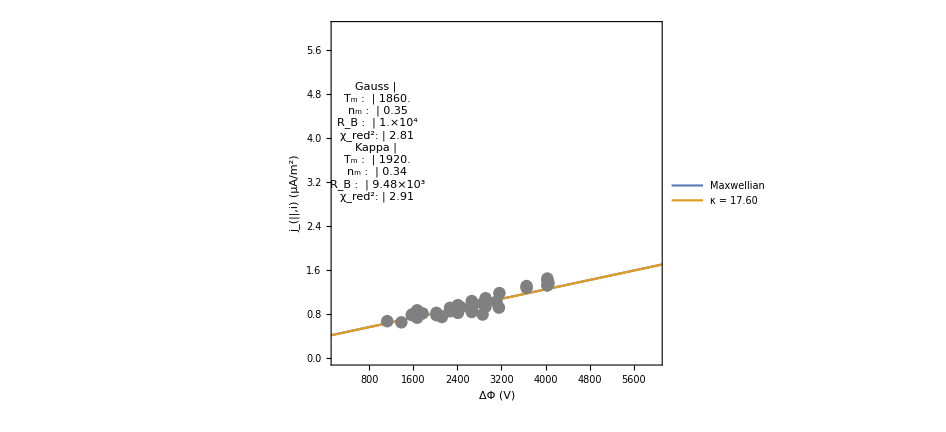

```mathematica
JVPlot=Show[Plot[{kFit[pot],gFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

### J_E-V plot

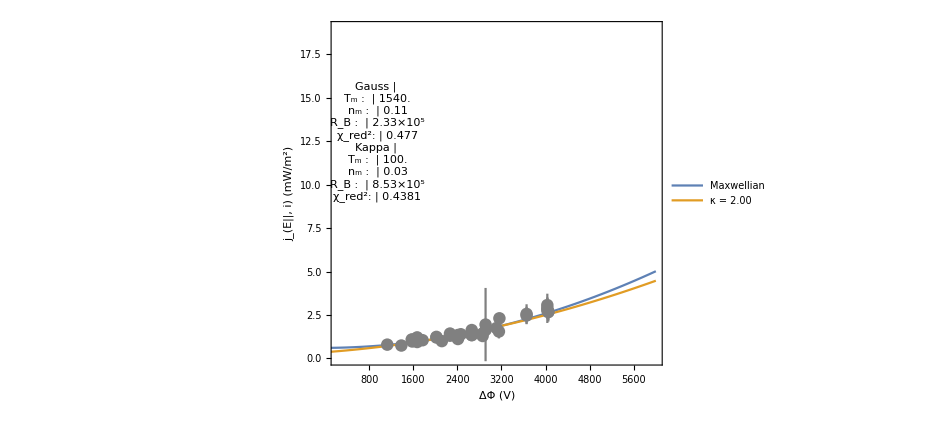

```mathematica
JeVPlot=Show[Plot[{kFitJeV[pot],gFitJeV[pot]},{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestJeVKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",Style[StringForm["J_E-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23],Epilog->Inset[JeVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jeErrData,PlotStyle->Gray]]
```

### Plots from combined fit

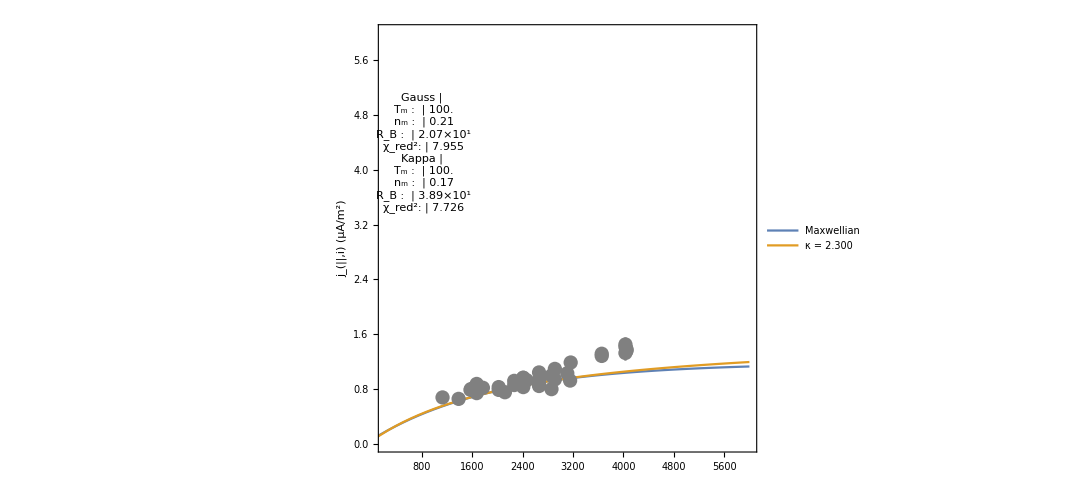
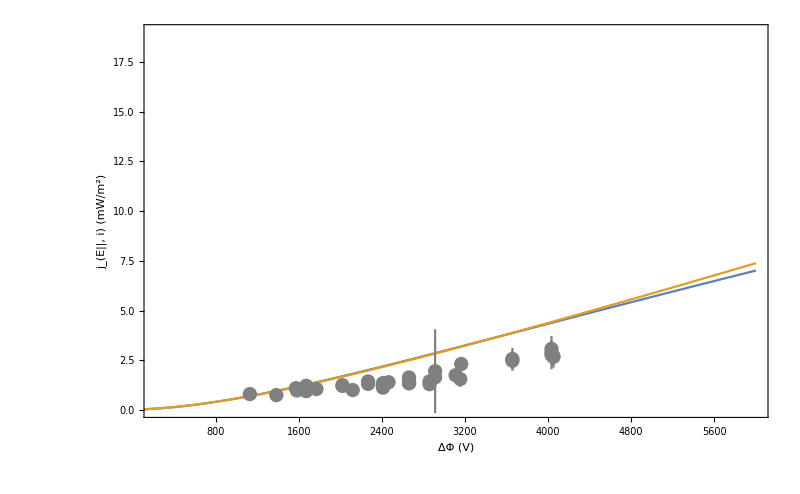

```mathematica
combPlot=Column[{combJVPlot,combJeVPlot}]
```

```mathematica
makePlots=1;
```

```mathematica
(*If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Export[dir<>JeVFilename,JeVPlot];Export[dir<>combJVFilename,combJVPlot];Export[dir<>combJeVFilename,combJeVPlot];Print["Done!"]]*)
```

```mathematica
If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Print[JeVFilename<>" ..."];Export[dir<>JeVFilename,JeVPlot];Print[combFilename<>" ..."];Export[dir<>combFilename,combPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/20180319/ ...

Orb11694__JeVFit__inds_162-198.png ...

Orb11694__combJVJeVFit__inds_162-198.png ...

Done!

Now everything at once

### Bounds

```mathematica
minFitT=5;
maxFitT=5000;
minFitRB=3;
maxFitRB=1000000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

### Initial guesses

```mathematica
kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;
gFitRB1init=10;
gFitRB2init=10;
```

### Setup indices

```mathematica
indsSeg1=Range[100,132];
```

```mathematica
indsSeg2=Range[137,150];
```

```mathematica
(*indsSeg2=Range[162,198]; (*Alt*)*)
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{jDataSeg1,jDataSeg2}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jErrDataSeg1,jErrDataSeg2}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jWtsSeg1,jWtsSeg2}=(1/(curErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

Energy flux data

```mathematica
{jeDataSeg1,jeDataSeg2}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeErrDataSeg1,jeErrDataSeg2}=(makeErrorData[pots[[#]],jes[[#]],jeErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeWtsSeg1,jeWtsSeg2}=(1/(jeErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

```mathematica
RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;
```

```mathematica
combDatSeg1 = Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y}];
```

```mathematica
combDatSeg2 = Join[jDataSeg2/.{x_,y_}->{1,x,y},jeDataSeg2/.{x_,y_}->{2,x,y}];
```

```mathematica
combWtsSeg1=jWtsSeg1~Join~jeWtsSeg1;
```

```mathematica
combWtsSeg2=jWtsSeg2~Join~jeWtsSeg2;
```

```mathematica
doubledDat= Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y},jDataSeg2/.{x_,y_}->{3,x,y},jeDataSeg2/.{x_,y_}->{4,x,y}];
```

```mathematica
doubledWts=jWtsSeg1~Join~jeWtsSeg1~Join~jWtsSeg2~Join~jeWtsSeg2;
```

### Now the doubled double model

```mathematica
kDoubledFitModel[set_,pot_,kFitRB1_,kFitRB2_,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==3,Evaluate@JVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa],set==4,Evaluate@JEVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa]]
```

```mathematica
gDoubledFitModel[set_,pot_,gFitRB1_,gFitRB2_,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==3,Evaluate@JVMaxwellian[pot,gFitRB2,gFitT,gFitN],set==4,Evaluate@JEVMaxwellian[pot,gFitRB2,gFitT,gFitN]]
```

```mathematica
kDoubledFit=NonlinearModelFit[doubledDat,{kDoubledFitModel[set,pot,kFitRB1,kFitRB2,kFitT,kFitN,kFitKappa],kDoubledConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB1,kFitRB1init},{kFitRB2,kFitRB2init},{kFitKappa,kFitKappainit}},{set,pot},Weights->doubledWts]
```

FittedModel[Which[set==1,(0.0266987 «4» Gamma[1+«18»])/((1-1/(«18»)) «1» Gamma[-1/2+«18»]),«4»,«1»,(0.0000268059 «6» Gamma[1+2.00683])/((-2+2.00683) (-1+2.00683) Gamma[-1/2+2.00683])]]

```mathematica
gDoubledFit=NonlinearModelFit[doubledDat,{gDoubledFitModel[set,pot,gFitRB1,gFitRB2,gFitT,gFitN],gDoubledConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB1,gFitRB1init},{gFitRB2,gFitRB2init}},{set,pot},Weights->doubledWts]
```

FittedModel[Which[set==1,«1»,«4»,set==4,0.0000268059 0.103323 2900.27 («18»)^(3/2) (2+pot/5.00001-ⅇ^(-pot/((-1+2900.27) «18»)) (2 (1-1/2900.27)+pot/5.00001))]]

```mathematica
kDOF=Length[doubledDat[[;;,1]]]-4;
```

```mathematica
gDOF=Length[doubledDat[[;;,1]]]-3;
```

```mathematica
{kDoubledN,kDoubledT,kDoubledRB1,kDoubledRB2,kDoubledKappa,kDoubledChi2red}=Values@kDoubledFit["BestFitParameters"]~Join~{Total[(kDoubledFit["FitResiduals"])^2*doubledWts]/kDOF};
```

```mathematica
{gDoubledN,gDoubledT,gDoubledRB1,gDoubledRB2,gDoubledChi2red}=Values@gDoubledFit["BestFitParameters"]~Join~{Total[(gDoubledFit["FitResiduals"])^2*doubledWts]/gDOF};
```

### Now setup plots

```mathematica
(*Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]*)
```

```mathematica
(*JVPlotSeg1=Show[Plot[{JVMaxwellian[pot,gDoubledRB1,gDoubledT,gDoubledN],JVKappa[pot,kDoubledRB1,kDoubledT,kDoubledN,kDoubledKappa]},{pot,minPot,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kDoubledKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,23]],ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]]*)
```

```mathematica
doubledRepl={gRB1->gDoubledRB1,gRB2->gDoubledRB2,gTm->gDoubledT,gnm->gDoubledN,gChi2->gDoubledChi2red,kRB1->kDoubledRB1,kRB2->kDoubledRB2,kTm->kDoubledT,knm->kDoubledN,kappa->kDoubledKappa,kChi2->kDoubledChi2red};
```

```mathematica
gDoubledVals1=(MapThread[NumberForm,{({gTm,gnm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB1,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals1=(MapThread[NumberForm,{({kTm,knm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB1,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

```mathematica
gDoubledVals2=(MapThread[NumberForm,{({gTm,gnm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB2,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals2=(MapThread[NumberForm,{({kTm,knm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB2,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

```mathematica
doubledParTable1=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gDoubledVals1~Join~{""}~Join~kDoubledVals1}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledParTable2=Text[Grid[Transpose[{{"Gauss"}~Join~parNames~Join~{"Kappa"}~Join~parNames,{""}~Join~gDoubledVals2~Join~{""}~Join~kDoubledVals2}],Alignment->".",Spacings->{0,vSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledTitle1=StringJoin@Riffle[time[[indsSeg1[[{1,-1}]]]],"–"];
```

```mathematica
doubledTitle2=StringJoin@Riffle[time[[indsSeg2[[{1,-1}]]]],"–"];
```

```mathematica
doubledFitJVPlot1=Plot[Evaluate@(({JVMaxwellian[pot,gRB1,gTm,gnm],JVKappa[pot,kRB1,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",doubledTitle1],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable1,Scaled[{0.12,0.7}]]];
```

```mathematica
doubledFitJeVPlot1=Plot[Evaluate@(({JEVMaxwellian[pot,gRB1,gTm,gnm],JEVKappa[pot,kRB1,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,23]];
```

```mathematica
doubledFitJVPlot2=Plot[Evaluate@(({JVMaxwellian[pot,gRB2,gTm,gnm],JVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->Map[(Style[#,23])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.doubledRepl),{3,3}]]}],Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",doubledTitle2],Bold,25]}},ImageSize->800,FrameStyle->Directive[Black,23],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable2,Scaled[{0.12,0.7}]]];
```

```mathematica
doubledFitJeVPlot2=Plot[Evaluate@(({JEVMaxwellian[pot,gRB2,gTm,gnm],JEVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,23]];
```

```mathematica
doubledJVPlot1=Show[doubledFitJVPlot1,ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot1=Show[doubledFitJeVPlot1,ErrorListPlot[jeErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJVPlot2=Show[doubledFitJVPlot2,ErrorListPlot[jErrDataSeg2,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot2=Show[doubledFitJeVPlot2,ErrorListPlot[jeErrDataSeg2,PlotStyle->Gray]];
```

### Now show plots

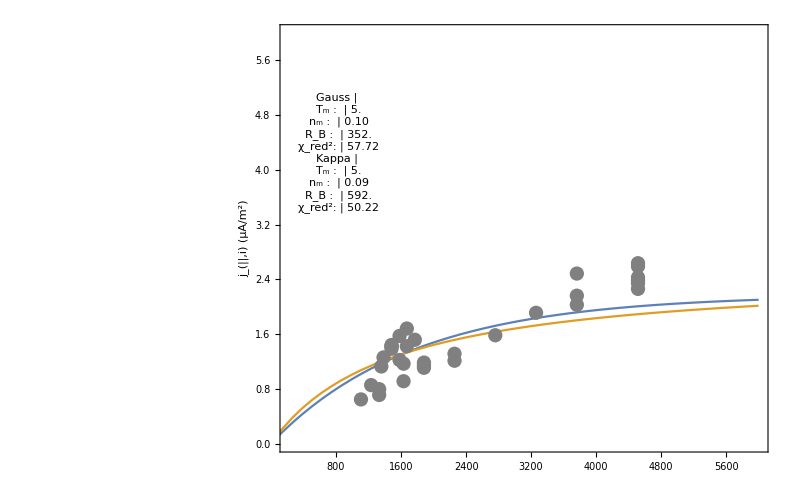
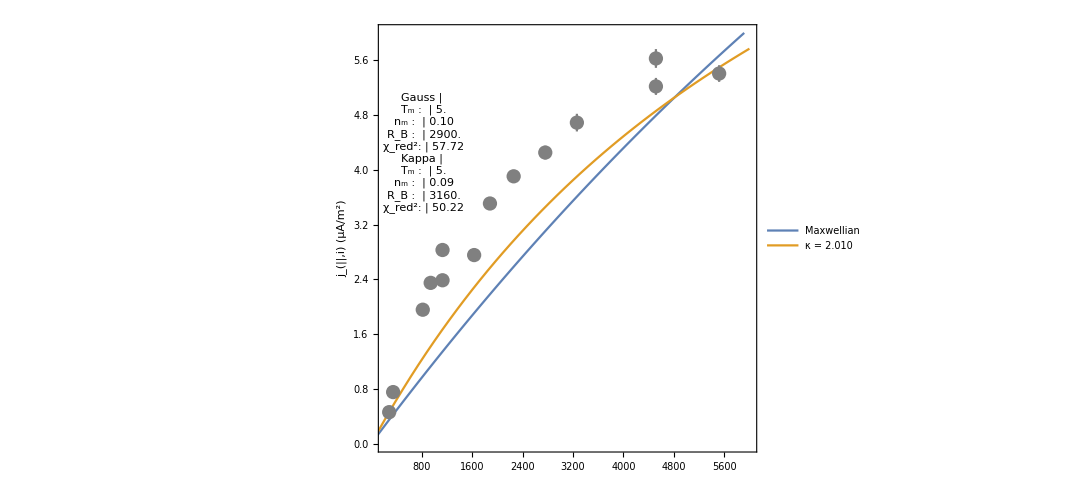
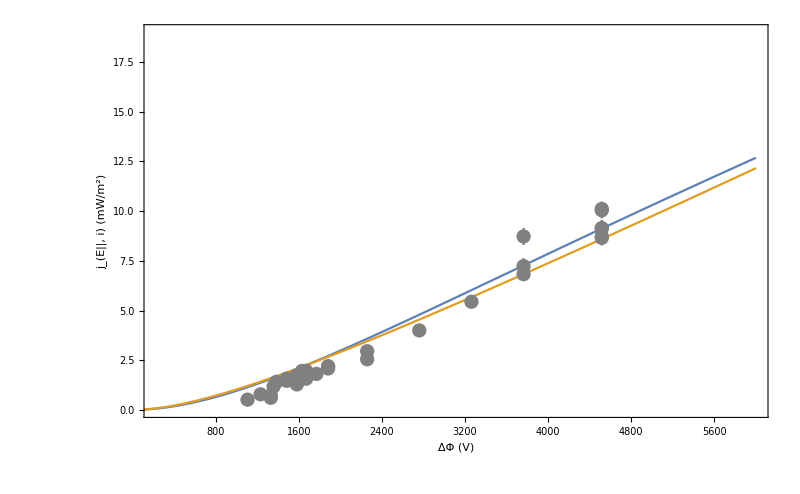
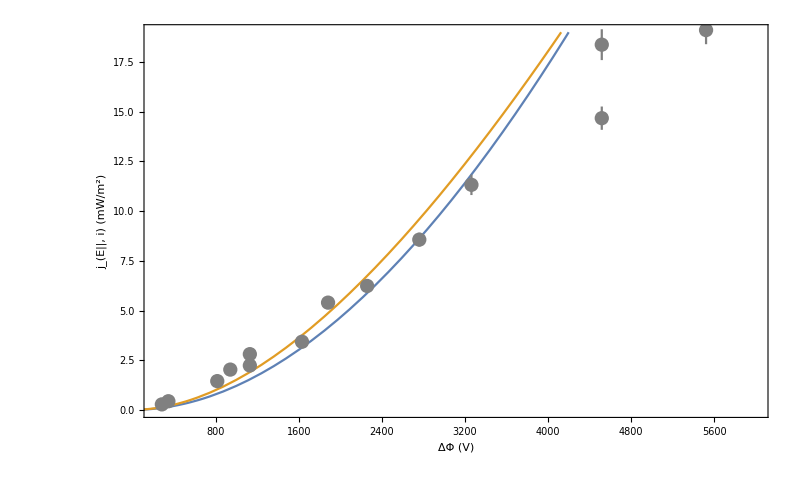
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
doubledPlot=Grid[{{doubledJVPlot1,doubledJVPlot2},{doubledJeVPlot1,doubledJeVPlot2}}]
```

Param tables

### J-V params

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.0788489 | 18.0635 | 0.0043651 | 0.996563
kFitT | 20.0084 | 211292. | 0.0000946954 | 0.999925
kFitRB | 999996. | 413.953 | 2415.72 | 1.33998×10^-53
kFitKappa | 1.5077 | 82.2571 | 0.0183292 | 0.985567

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.737783 | 2.50754 | 0.294226 | 0.771617
gFitT | 20. | 189.449 | 0.10557 | 0.916976
gFitRB | 336621. | 1.19817×10^10 | 0.0000280946 | 0.999978

### J_E-V params

```mathematica
kFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.590468 | 12.8417 | 0.0459806 | 0.963806
kFitT | 20.0001 | 209.717 | 0.0953669 | 0.925022
kFitRB | 239189. | 4.5854×10^9 | 0.0000521631 | 0.999959
kFitKappa | 2.43713 | 84.7723 | 0.0287491 | 0.977365

```mathematica
gFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.762078 | 0.387809 | 1.96508 | 0.063448
gFitT | 20. | 47.5033 | 0.421023 | 0.678228
gFitRB | 330538. | 6.09865×10^9 | 0.0000541986 | 0.999957

### Params from combined fit

```mathematica
kCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitRB | 805633. | 8.95543×10^9 | 0.0000899603 | 0.999929
kFitT | 20. | 157.058 | 0.127342 | 0.899278
kFitN | 0.491447 | 1.8178 | 0.270352 | 0.788213
kFitKappa | 2.0396 | 0.791263 | 2.57765 | 0.0135471

```mathematica
gCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitRB | 450860. | 4.64319×10^9 | 0.0000971014 | 0.999923
gFitT | 20. | 30.7434 | 0.650545 | 0.518801
gFitN | 0.738934 | 0.408339 | 1.80961 | 0.0773503